KL problemのチェック

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=1/(6 ReT^2)ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT]))

```mathematica
V=FullSimplify[V/.{ImT->0,w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(ⅇ^(-2 (a+b) ReT) (b B ⅇ^(a ReT)+a A ⅇ^(b ReT)) (A ⅇ^(b ReT) (3+a ReT)+B ⅇ^(a ReT) (3+b ReT)-3 ⅇ^((a+b) ReT) Abs[Abs[(a A)/(b B)]^(-b/(a-b)) (B+A Abs[(b B)/(a A)])]))/(6 ReT^2)

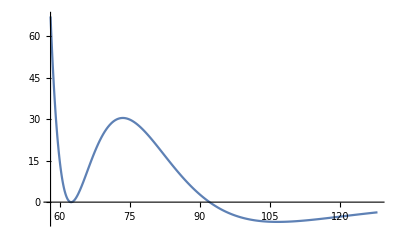

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=58;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+70},WorkingPrecision->100,PlotPoints->200]
```

```mathematica
A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))/.{a->vala,b->valb,A->valA,B->valB}
```

0.000198152

KKLT

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+w0) (A ⅇ^(-a T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-(3 (A ⅇ^(-a T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-(3 (A ⅇ^(-a T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)+3 ⅇ^(a ReT) w0 Cos[a ImT]))/(6 ReT^2)

```mathematica
V=FullSimplify[V/.{ImT->Pi/a,w0->Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)-3 ⅇ^(a ReT) Abs[A Abs[(a A)/(b B)]^(a/(-a+b))+B Abs[(a A)/(b B)]^(b/(-a+b))]))/(6 ReT^2)

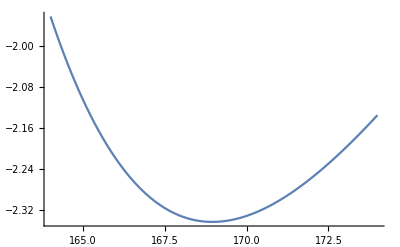

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=164;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
```

メゾンMを入れたポテンシャルのmoduli stabilization

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T]+μ X M+α Λ^3*Exp[-c T]/M^(1/(N-1));
W̄=W/.{T->T̄,X->X̄,M->M̄};

K=-3Log[T+T̄]+Z X*X̄+μ M*M̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T M̄]=D[K,T,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,X,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M T̄]=D[K,M,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄],Subscript[K, T M̄]},{Subscript[K, X T̄],Subscript[K, X X̄],Subscript[K, X M̄]},{Subscript[K, M T̄],Subscript[K, M X̄],Subscript[K, M M̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, T M̄]=Kinv[[1,3]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];
Subscript[invK, X M̄]=Kinv[[2,3]];
Subscript[invK, M T̄]=Kinv[[3,1]];
Subscript[invK, M X̄]=Kinv[[3,2]];
Subscript[invK, M M̄]=Kinv[[3,3]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, T M̄]*(DTW)*(OverBar[DMW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M T̄]*(DMW)*(OverBar[DTW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
Print["V=",vtemp];

V=ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];

Print["time: ",AbsoluteTime[]-inittime];
```

V=1/(T+T̄)^3 ⅇ^(M μ M̄+X Z X̄) (-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+N)) α Λ^3+M X μ) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄)+((M μ+Z (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+N)) α Λ^3+M X μ) X̄) (μ M̄+X Z (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄)))/Z+1/μ(-(ⅇ^(-c T) M^(-1-1/(-1+N)) α Λ^3)/(-1+N)+X μ+μ (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+N)) α Λ^3+M X μ) M̄) (-(ⅇ^(-c T̄) α Λ^3 (M̄)^(-1-1/(-1+N)))/(-1+N)+μ X̄+M μ (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄))+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-c ⅇ^(-c T) M^(-1/(-1+N)) α Λ^3-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+N)) α Λ^3+M X μ))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-c ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+N))-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄))/(T+T̄)))

time: 3.445491

陳さんの修論の結果を再現

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+μ X M+α Λ^3/M^(1/(N-1));
W̄=W/.{X->X̄,M->M̄};

K=Z X*X̄+μ M*M̄;
Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, X X̄],Subscript[K, X M̄]},{Subscript[K, M X̄],Subscript[K, M M̄]}};
Kinv=Inverse[Kmat];

Subscript[invK, X X̄]=Kinv[[1,1]];
Subscript[invK, X M̄]=Kinv[[1,2]];
Subscript[invK, M X̄]=Kinv[[2,1]];
Subscript[invK, M M̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
Print["V=",vtemp];

V=ComplexExpand[vtemp/.{X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];

Print["time: ",AbsoluteTime[]-inittime];
```

V=ⅇ^(M μ M̄+X Z X̄) (-3 (w0+M^(-1/(-1+N)) α Λ^3+M X μ) (w0+α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄)+((M μ+Z (w0+M^(-1/(-1+N)) α Λ^3+M X μ) X̄) (μ M̄+X Z (w0+α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄)))/Z+((-(M^(-1-1/(-1+N)) α Λ^3)/(-1+N)+X μ+μ (w0+M^(-1/(-1+N)) α Λ^3+M X μ) M̄) (-(α Λ^3 (M̄)^(-1-1/(-1+N)))/(-1+N)+μ X̄+M μ (w0+α Λ^3 (M̄)^(-1/(-1+N))+μ M̄ X̄)))/μ)

time: 0.5798341

```mathematica
valα=;
valN=;
valΛ=;
valλ=;
valC=;
valZ=;
```